```mathematica
(* Problem #1 *)
```

```mathematica
f[K_,T_]:=T==(1+K)*(1-Exp[-T])
```

```mathematica
NSolve[f[k*V/g, k*T], T]//Quiet
```

{{T→(1. g+1. k V+1. g ProductLog[-(0.367879 ⅇ^(-(1. k V)/g) (1. g+1. k V))/g])/(g k)}}

```mathematica
t[k_]:=(1. g+1. k V+1. g ProductLog[-(0.36787944117144233 ⅇ^(-(1. k V)/g) (1. g+1. k V))/g])/(g k)
```

```mathematica
Limit[f[(k*V)/g,k*T],k->0]
```

T (T-(2 V)/g)==0

```mathematica
Solve[T (T-(2 V)/g)==0,T]
```

{{T→0},{T→(2 V)/g}}

```mathematica
R0=(U*V*2)/g
```

(2 U V)/g

```mathematica
R[K_,T_]:=T/(2K*(K+1))R0
Limit[R[(k*V)/g,k*(2 V)/g],k->0]
```

(2 U V)/g

```mathematica
Manipulate[Plot[{R[K,(K*g)/V*t[(K*g)/V]]/R0}, {K,0,L}],{L,0.01,100}]
```

```mathematica
(* Problem #2*)
```

```mathematica
DSolve[{m*D[v[t],t]==-m*g-α*v[t]^2, v[0]==v0}, v[t],t]//Quiet
```

{{v[t]→(√g √m Tan[(-√g t √α+√m ArcTan[(v0 √α)/(√g √m)])/(√m)])/(√α)}}

```mathematica
(* Expanding ArcTan with Taylor series *)

Exptan=((v0 √α)/(√g √m))-((v0 √α)/(√g √m))^3/3
```

(v0 √α)/(√g √m)-(v0^3 α^(3/2))/(3 g^(3/2) m^(3/2))

```mathematica
vel[t_]:= (√g √m Tan[(-√g t √α+√m *Exptan)/(√m)])/(√α)
```

```mathematica
Integrate[vel[t],t]
```

(m Log[Cos[(√α (3 g^2 m t-3 g m v0+v0^3 α))/(3 g^(3/2) m^(3/2))]])/α

```mathematica
x[t_]:=(m Log[Cos[(√α (3 g^2 m t-3 g m v0+v0^3 α))/(3 g^(3/2) m^(3/2))]])/α
NSolve[x[0]+c ==0,c]               (* This is to set the position at time 0 to be 0 *)
```

{{c→-(1. m Log[Cos[(0.333333 √α (-3. g m v0+v0^3 α))/(g^(3/2) m^(3/2))]])/α}}

```mathematica
c=-(1. m Log[Cos[(0.3333333333333333 √α (-3. g m v0+v0^3 α))/(g^(3/2) m^(3/2))]])/α
```

-(1. m Log[Cos[(0.333333 √α (-3. g m v0+v0^3 α))/(g^(3/2) m^(3/2))]])/α

```mathematica
y[t_]:=x[t]+ c
```

```mathematica
y[t]
```

(m Log[Cos[(√α (3 g^2 m t-3 g m v0+v0^3 α))/(3 g^(3/2) m^(3/2))]])/α-(1. m Log[Cos[(0.333333 √α (-3. g m v0+v0^3 α))/(g^(3/2) m^(3/2))]])/α

```mathematica
NSolve[vel[t]==0,t]//Quiet

 (* this will give us the time of the maximum Hight H(α) *)
```

{{t→(1. v0)/g-(0.333333 v0^3 α)/(g^2 m)}}

```mathematica
Htime[α_]:=(1. v0)/g-(1/3 v0^3 α)/(g^2 m)
```

```mathematica
Limit[Htime[α],α->0]

 (* This shows that without air resistance, the time for maximum height will be the same as PHYS101 Equation i.e. V0/g *)
```

(1. v0)/g

```mathematica
H[α_]:=y[Htime[α]]
```

```mathematica
g=9.8
v0=10
m=5

(* setting random numbers for v0, m to be able to plot *)
```

9.8

10

5

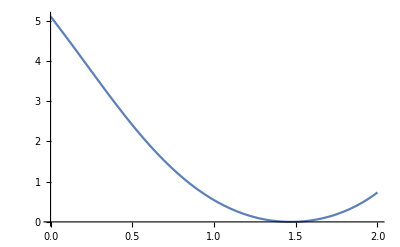

```mathematica
Plot[H[α], {α,0, 2}]
```

```mathematica
(*Checking whether the limit of H(α) as α->0 agrees with y=v0*t-1/2 g*t^2 (no air resistance) *)

Limit[H[α], α->0] - (v0*Htime[0]-1/2*g*Htime[0]^2)
```

0.